# Εργασία 4η

## 1η Άσκηση

Δίνεται ένα τυχαίο δείγμα 9 μετρήσεων από έναν πληθυσμό με κανονική κατανομή N(μ, σ=1) και θέλουμε να ελέγξουμε την υπόθεση Η_0: μ = 20 ως προς την εναλλακτική Η_1: μ = 22, χρησιμοποιώντας το ακόλουθο κριτήριο: απορρίπτουμε την Η_0 αν x̄ ≥ 21. Υπολογίστε τα σφάλματα Τύπου Ι, ΙΙ καθώς και τη δύναμη του κριτηρίου. Πόσο είναι το μέγεθος του τεστ;

Λύση

```mathematica
ClearAll["Global`*"];
inches=72;
n = 9;
σ=1;
```

```mathematica
N[1-CDF[NormalDistribution[20,σ/3],21]]
```

0.0013499

```mathematica
N[CDF[NormalDistribution[22,σ/3],21]]
```

0.0013499

```mathematica
1-NIntegrate[1/(√(2π)/3)E^(-(x-22)^2/(2/9)),{x,-Infinity,21}]
```

0.99865

```mathematica
power = 1 - %%
```

0.99865

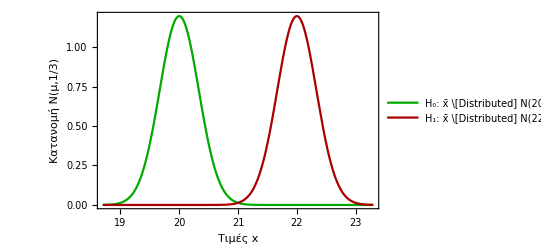

```mathematica
plt12=Plot[{PDF[NormalDistribution[20,1/3],x],PDF[NormalDistribution[22,1/3],x]},{x,18.7,23.3},PlotRange->All,PlotLegends->{"H_0: x̄ \[Distributed] N(20,1/3)","H_1: x̄ \[Distributed] N(22,1/3)"},PlotStyle->{{Darker[Green]},{Darker[Red]}},Frame->True,FrameLabel->{"Τιμές x","Κατανομή Ν(μ,1/3)"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex1-1.png",Show[plt12,ImageSize->15 inches]];
```

## 2η Άσκηση

Οι πυκνότητες πιθανότητας δύο τυχαίων μεταβλητών καταγράφονται στον παρακάτω πίνακα, οργανωμένες σε διαμέρηση (bins) μεγέθους 0.5 από −3.0 έως 3.0. Να κάνετε τα διαγράμματα των ιστογραμμάτων και να εξετάσετε αν οι μεταβλητές αυτές ακολουθούν την τυποποιημένη κανονική κατανομή (να συγκρίνετε την τιμή των δεδομένων σε κάθε bin με την θεωρητική πρόβλεψη για το σημείο στο κέντρο του bin). Χρησιμοποιήστε το Pearson’s-χ2 τεστ με α=0.1 και το RUN τεστ. 
										BIN | ΟΡΙΑ | PDF1 × dx | PDF2 × dx
1 | [-3.0,-2.5] | 0.0042±0.0009 | 0.0056±0.0011
2 | [-2.5,-2.0] | 0.0186±0.0019 | 0.0214±0.0021
3 | [-2.0,-1.5] | 0.0422±0.0029 | 0.0422±0.0029
4 | [-1.5,-1.0] | 0.0926±0.0043 | 0.0844±0.0041
5 | [-1.0,-0.5] | 0.1456±0.0054 | 0.1296±0.0051
6 | [-0.5,0.0] | 0.1886±0.0061 | 0.1660±0.0058
7 | [0.0,0.5] | 0.1866±0.0061 | 0.1736±0.0059
8 | [0.5,1.0] | 0.1514±0.0055 | 0.1536±0.0055
9 | [1.0,1.5] | 0.0894±0.0042 | 0.1072±0.0046
10 | [1.5,2.0] | 0.0546±0.0033 | 0.0626±0.0035
11 | [2.0,2.5] | 0.0176±0.0019 | 0.0340±0.0026
12 | [2.5,3.0] | 0.0066±0.0011 | 0.0136±0.0016

Λύση

```mathematica
ClearAll["Global`*"];
inches=72;
α=0.1;
```

```mathematica
X={-2.75,-2.25,-1.75,-1.25,-0.75,-0.25,0.25,0.75,1.25,1.75,2.25,2.75};
```

```mathematica
LPDF1={
{-2.75,0.0042/0.5±0.0009/0.5},
{-2.25,0.0186/0.5±0.0019/0.5},
{-1.75,0.0422/0.5±0.0029/0.5},
{-1.25,0.0926/0.5±0.0043/0.5},
{-0.75,0.1456/0.5±0.0054/0.5},
{-0.25,0.1886/0.5±0.0061/0.5},
{0.25,0.1866/0.5±0.0061/0.5},
{0.75,0.1514/0.5±0.0055/0.5},
{1.25,0.0894/0.5±0.0042/0.5},
{1.75,0.0546/0.5±0.0033/0.5},
{2.25,0.0176/0.5±0.0019/0.5},
{2.75,0.0066/0.5±0.0011/0.5}
};
PDF1={
{-2.75,0.0042/0.5},
{-2.25,0.0186/0.5},
{-1.75,0.0422/0.5},
{-1.25,0.0926/0.5},
{-0.75,0.1456/0.5},
{-0.25,0.1886/0.5},
{0.25,0.1866/0.5},
{0.75,0.1514/0.5},
{1.25,0.0894/0.5},
{1.75,0.0546/0.5},
{2.25,0.0176/0.5},
{2.75,0.0066/0.5}
};
```

```mathematica
e1={0.0009/0.5,0.0019/0.5,0.0029/0.5,0.0043/0.5,0.0054/0.5,0.0061/0.5,0.0061/0.5,0.0055/0.5,0.0042/0.5,0.0033/0.5,0.0019/0.5,0.0011/0.5};
```

```mathematica
w1 = 1/e1^2;
```

```mathematica
LPDF2={
{-2.75,0.0056/0.5±0.0011/0.5},
{-2.25,0.0214/0.5±0.0021/0.5},
{-1.75,0.0422/0.5±0.0029/0.5},
{-1.25,0.0844/0.5±0.0041/0.5},
{-0.75,0.1296/0.5±0.0051/0.5},
{-0.25,0.1660/0.5±0.0058/0.5},
{0.25,0.1736/0.5±0.0059/0.5},
{0.75,0.1536/0.5±0.0055/0.5},
{1.25,0.1072/0.5±0.0046/0.5},
{1.75,0.0626/0.5±0.0035/0.5},
{2.25,0.0340/0.5±0.0026/0.5},
{2.75,0.0136/0.5±0.0016/0.5}
};
PDF2={
{-2.75,0.0056/0.5},
{-2.25,0.0214/0.5},
{-1.75,0.0422/0.5},
{-1.25,0.0844/0.5},
{-0.75,0.1296/0.5},
{-0.25,0.1660/0.5},
{0.25,0.1736/0.5},
{0.75,0.1536/0.5},
{1.25,0.1072/0.5},
{1.75,0.0626/0.5},
{2.25,0.0340/0.5},
{2.75,0.0136/0.5}
};
```

```mathematica
e2={0.0011/0.5,0.0021/0.5,0.0029/0.5,0.0041/0.5,0.0051/0.5,0.0058/0.5,0.0059/0.5,0.0055/0.5,0.0046/0.5,0.0035/0.5,0.0026/0.5,0.0016/0.5};
```

```mathematica
w2 = 1/e2^2;
```

```mathematica
LP1 =ListPlot[LPDF1,Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"PDF1"}];
```

```mathematica
LP2 =ListPlot[LPDF2,PlotStyle->Gray,Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"PDF2"}];
```

```mathematica
P1=Plot[PDF[NormalDistribution[],x],{x,-3.5,3.5},PlotRange->All,PlotStyle->Red,Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"N(0,1)"}];
```

```mathematica
PDF1y=ParallelTable[PDF1[[i]][[2]],{i,1,Length[PDF1]}]
```

{0.0084,0.0372,0.0844,0.1852,0.2912,0.3772,0.3732,0.3028,0.1788,0.1092,0.0352,0.0132}

```mathematica
PDF2y=ParallelTable[PDF2[[i]][[2]],{i,1,Length[PDF2]}];
```

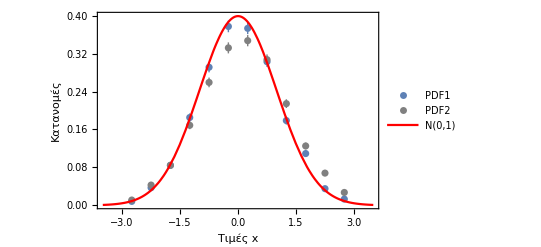

```mathematica
plt12=Show[LP1,LP2,P1,PlotRange->All]

Export["ex2-1.png",Show[plt12,ImageSize->15 inches]];
```

```mathematica
pvaluechi1 =SurvivalFunction[ChiSquareDistribution[Length[PDF1y]],Total[w1(PDF[NormalDistribution[0,1],X]- PDF1y)^2]]
If[pvaluechi1<α,True,False]
```

0.0412377

True

```mathematica
Total[w1(PDF[NormalDistribution[0,1],X]- PDF1y)^2]
```

21.6824

```mathematica
pvaluechi2 =SurvivalFunction[ChiSquareDistribution[Length[PDF2y]],Total[w2(PDF[NormalDistribution[0,1],X]- PDF2y)^2]]
If[pvaluechi2<α,True,False]
```

4.23648×10^-33

True

```mathematica
Total[w2(PDF[NormalDistribution[0,1],X]- PDF2y)^2]
```

184.884

```mathematica
Np1=Length[Pick[PDF[NormalDistribution[0,1],X] - PDF1y ,Positive[PDF[NormalDistribution[0,1],X] - PDF1y ]]];
Nm1= Length[PDF1y]-Np1;
r1 = 8;
Er1= 1+(2*Np1*Nm1)/(Np1+Nm1);
Vr1 = (2*Np1*Nm1)(2Np1 Nm1 - Np1 - Nm1)/((Np1 + Nm1)^2(Np1+Nm1-1))//N;
z1 = (r1- Er1)/Sqrt[Vr1]//N;
pvaluert1=2*N[1-CDF[NormalDistribution[0,1],Abs[z1]]]
```

0.544827

```mathematica
PDF[NormalDistribution[0,1],X] - PDF1y
```

{0.000693563,-0.00546035,0.00187732,-0.00255091,0.00993743,0.00946812,0.0134681,-0.00166257,0.00384909,-0.0229227,-0.00346035,-0.00410644}

```mathematica
Np2= Length[Pick[PDF[NormalDistribution[0,1],X] - PDF2y ,Positive[PDF[NormalDistribution[0,1],X] - PDF2y ]]];
Nm2= Length[PDF2y]-Np2;
r2 = 3;
Er2= 1+(2*Np2*Nm2)/(Np2+Nm2)//N;
Vr2 = (2*Np2*Nm2)(2Np2 Nm2 - Np2 - Nm2)/((Np2 + Nm2)^2(Np2+Nm2-1))//N;
z2 = (r2- Er2)/Sqrt[Vr2]//N;
pvaluert2=2*N[1-CDF[NormalDistribution[0,1],Abs[z2]]]
```

0.016649

```mathematica
Totpvalue1 = pvaluechi1*pvaluert1*(1 - Log[pvaluechi1*pvaluert1])
```

0.107747

```mathematica
Totpvalue2 = pvaluechi2*pvaluert2*(1 - Log[pvaluechi2*pvaluert2])
```

5.61704×10^-33

## 3η Άσκηση

Δύο μηχανές M_1  και M_2 αυτόματης συσκευασίας έχουν ρυθμιστεί έτσι ώστε να γεμίζουν πακέτα βάρους 1 kg. Υπάρχουν υπόνοιες ότι οι δύο μηχανές δεν λειτουργούν ομοιόμοφα ως προς τη μάζα του περιεχομένου. Για το λόγο αυτό, λαμβάνονται 100 πακέτα από την παραγωγή κάθε μηχανής και βρίσκεται ότι οι δειγματικοί μέσοι είναι αντίστοιχα 1.07 και 1.18 kg. Από προηγούμενες παρατηρήσεις γνωρίζουμε ότι σ_1 = 0.10 και σ_2 = 0.12 kg. (α) Υπάρχει πράγματι διαφορά μεταξύ των δύο μηχανών, σε επίπεδο σημαντικότητας 0.05; (β) Να βρείτε την ισχύ του τεστ του (α) ερωτήματος όταν η μέση μάζα του πακέτου της μηχανής M_2 είναι κατά δ kg μεγαλύτερη από αυτή της M_1.

Λύση

```mathematica
(* Σελ.16 Lecture 6: 2η περίπτωση *)
```

```mathematica
ClearAll["Global`*"];
inches=72;
α = 0.05;
σ1 = 0.1;
σ2 = 0.12;
μ1 = 1.07;
μ2 = 1.18;
n=100;
SD = Sqrt[(σ1 ^2)/n+σ2^2/n]
```

0.0156205

```mathematica
F =( σ2 /σ1)^2
```

1.44

```mathematica
Fratio = InverseCDF[FRatioDistribution[n-1,n-1],1- α/2]
```

1.48623

```mathematica
If[F <Fratio,"Η H_0 ΔΕΝ απορρίπτεται (σ1 = σ2)","Η H_0  απορρίπτεται (σ1 ≠ σ2)"]
```

Η H_0 ΔΕΝ απορρίπτεται (σ1 = σ2)

```mathematica
S = Sqrt[((n -1)σ1^2 + (n-1)σ2^2)/(n+n - 2)]
```

0.110454

```mathematica
z1 = (μ1 - μ2)/(S*Sqrt[1/n+1/n])
```

-7.04203

```mathematica
za1 = Quantile[NormalDistribution[0,1],α/2]
```

-1.95996

```mathematica
"Η H_0 δεν απορρίπτεται (μ1 = μ2), αφού C = (-∞, -za/2)∪(za/2,+∞)"
```

Η H_0 δεν απορρίπτεται (μ1 = μ2), αφού C = (-∞, -za/2)∪(za/2,+∞)

```mathematica
δ = 0.0001
```

0.0001

```mathematica
z2 = (μ1 - μ2)/(S*Sqrt[1/n+1/n])
```

-7.04203

```mathematica
za = Quantile[NormalDistribution[0,1],α/2]
```

-1.95996

```mathematica
β=CDF[NormalDistribution[δ/(S*Sqrt[1/n+1/n]),1],za]
```

0.0246282

```mathematica
power = 1 - β
```

0.975372

## 4η Άσκηση

Δύο διαφορετικά ηλεκτρονικά όργανα Α και Β χρησιμοποιούνται για την μέτρηση της πίεσης του ματιού. Ενδιαφερόμαστε να συγκρίνουμε τα όργανα αυτά ως προς την ποιότητά τους, δηλαδή να συγκρίνουμε την μεταβλητότητα επανειλημμένων μετρήσεων στο ίδιο μάτι, την ίδια περίπου χρονική στιγμή. Με το όργανο Α κάναμε 10 μετρήσεις και βρήκαμε διασπορά δείγματος S_Α^2=1.25, ενώ με το όργανο Β κάναμε 8 μετρήσεις με διασπορά δείγματος S_Β^2=0.28. Να ελέγξετε την υπόθεση ότι τα δύο όργανα έχουν ίδια ποιότητα (ακρίβεια μετρήσεων) σε επίπεδο σημαντικότητας 10%.

Λύση

```mathematica
(* Σελ.16 pdf: H0: σ1 = σ2, H1 = σ1 ≠ σ2 *)
```

```mathematica
ClearAll["Global`*"];
inches=72;
SA2 = 1.25;
SB2 = 0.28;
α = 0.1;
nA =10;
nB = 8;
```

```mathematica
F =SB2/SA2
```

0.224

```mathematica
Fratio=InverseCDF[FRatioDistribution[nA-1,nB-1],1-(α/2)]
```

3.67667

```mathematica
If[F <Fratio,"Έχουν την ίδια ποιότητα (σ1 = σ2)","ΔΕΝ έχουν την ίδια ποιότητα (σ1 ≠ σ2)"]
```

Έχουν την ίδια ποιότητα (σ1 = σ2)

## 5η Άσκηση

Έστω δύο τυχαίες μεταβλητές που ακολουθούν αντίστοιχα ομοιόμορφη κατανομή στο διάστημα [0, 1] και τυποποιημένη κανονική κατανομή N(0,1). Να παράξετε ένα τυχαίο σύνολο n=10 τιμών για κάθε μεταβλητή και να παραστήσετε γραφικά τις δύο αθροιστικές κατανομές (σε διαφορετικά διαγράμματα) συγκρινόμενες με τις αντίστοιχες θεωρητικές. Πόση είναι σε κάθε περίπτωση η μέγιστη απόλυτη απόκλιση D; Να επαναλάβετε τη διαδικασία 10000 φορές και να κάνετε την κατανομή της ποσότητας √n·D για κάθε περίπτωση. Αποφανθείτε για την συμβατότητα των κατανομών (π.χ. με τεστ χ^2). Στη συνέχεια να επαναλάβετε όλα τα βήματα παράγοντας τυχαία σύνολα 100 τιμών.

Λύση

```mathematica
ClearAll["Global`*"];
n=10;
ndot = 100;
Y = RandomVariate[UniformDistribution[{0,1}],n];
X = RandomVariate[NormalDistribution[0,1],n];
Y100 = RandomVariate[UniformDistribution[{0,1}],ndot];
X100 = RandomVariate[NormalDistribution[0,1],ndot];
inches=72;
rline1 = n - 2;
rline2 = ndot - 2;
```

```mathematica
normalcdf = CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

```mathematica
uniformcdf = CDF[UniformDistribution[{0,1}],x]
```

Piecewise[{{x, 0≤x≤1}, {1, x>1}, {0, True}}]

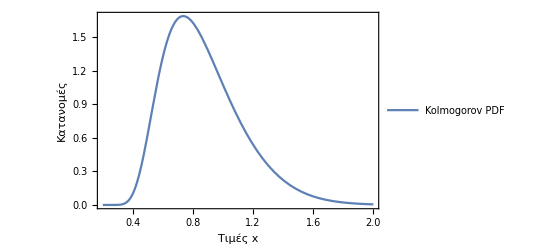

```mathematica
Sqrt[2 Pi]/x * Sum[Exp[-(2 k -1)^2 Pi^2/(8 x^2)],{k,1,n}];
f[x_] := Sqrt[2 Pi]/x * Sum[Exp[-(2 k -1)^2 Pi^2/(8 x^2)],{k,1,50}];
f1=D[Quiet[Sqrt[2 Pi]/x * Sum[Exp[-(2 k -1)^2 Pi^2/(8 x^2)],{k,1,50}]],x];
F[x_]:=-1/x^2(ⅇ^(-(9801 π^2)/(8 x^2))+ⅇ^(-(9409 π^2)/(8 x^2))+ⅇ^(-(9025 π^2)/(8 x^2))+ⅇ^(-(8649 π^2)/(8 x^2))+ⅇ^(-(8281 π^2)/(8 x^2))+ⅇ^(-(7921 π^2)/(8 x^2))+ⅇ^(-(7569 π^2)/(8 x^2))+ⅇ^(-(7225 π^2)/(8 x^2))+ⅇ^(-(6889 π^2)/(8 x^2))+ⅇ^(-(6561 π^2)/(8 x^2))+ⅇ^(-(6241 π^2)/(8 x^2))+ⅇ^(-(5929 π^2)/(8 x^2))+ⅇ^(-(5625 π^2)/(8 x^2))+ⅇ^(-(5329 π^2)/(8 x^2))+ⅇ^(-(5041 π^2)/(8 x^2))+ⅇ^(-(4761 π^2)/(8 x^2))+ⅇ^(-(4489 π^2)/(8 x^2))+ⅇ^(-(4225 π^2)/(8 x^2))+ⅇ^(-(3969 π^2)/(8 x^2))+ⅇ^(-(3721 π^2)/(8 x^2))+ⅇ^(-(3481 π^2)/(8 x^2))+ⅇ^(-(3249 π^2)/(8 x^2))+ⅇ^(-(3025 π^2)/(8 x^2))+ⅇ^(-(2809 π^2)/(8 x^2))+ⅇ^(-(2601 π^2)/(8 x^2))+ⅇ^(-(2401 π^2)/(8 x^2))+ⅇ^(-(2209 π^2)/(8 x^2))+ⅇ^(-(2025 π^2)/(8 x^2))+ⅇ^(-(1849 π^2)/(8 x^2))+ⅇ^(-(1681 π^2)/(8 x^2))+ⅇ^(-(1521 π^2)/(8 x^2))+ⅇ^(-(1369 π^2)/(8 x^2))+ⅇ^(-(1225 π^2)/(8 x^2))+ⅇ^(-(1089 π^2)/(8 x^2))+ⅇ^(-(961 π^2)/(8 x^2))+ⅇ^(-(841 π^2)/(8 x^2))+ⅇ^(-(729 π^2)/(8 x^2))+ⅇ^(-(625 π^2)/(8 x^2))+ⅇ^(-(529 π^2)/(8 x^2))+ⅇ^(-(441 π^2)/(8 x^2))+ⅇ^(-(361 π^2)/(8 x^2))+ⅇ^(-(289 π^2)/(8 x^2))+ⅇ^(-(225 π^2)/(8 x^2))+ⅇ^(-(169 π^2)/(8 x^2))+ⅇ^(-(121 π^2)/(8 x^2))+ⅇ^(-(81 π^2)/(8 x^2))+ⅇ^(-(49 π^2)/(8 x^2))+ⅇ^(-(25 π^2)/(8 x^2))+ⅇ^(-(9 π^2)/(8 x^2))+ⅇ^(-π^2/(8 x^2))) √(2 π)+1/x √(2 π) ((9801 ⅇ^(-(9801 π^2)/(8 x^2)) π^2)/(4 x^3)+(9409 ⅇ^(-(9409 π^2)/(8 x^2)) π^2)/(4 x^3)+(9025 ⅇ^(-(9025 π^2)/(8 x^2)) π^2)/(4 x^3)+(8649 ⅇ^(-(8649 π^2)/(8 x^2)) π^2)/(4 x^3)+(8281 ⅇ^(-(8281 π^2)/(8 x^2)) π^2)/(4 x^3)+(7921 ⅇ^(-(7921 π^2)/(8 x^2)) π^2)/(4 x^3)+(7569 ⅇ^(-(7569 π^2)/(8 x^2)) π^2)/(4 x^3)+(7225 ⅇ^(-(7225 π^2)/(8 x^2)) π^2)/(4 x^3)+(6889 ⅇ^(-(6889 π^2)/(8 x^2)) π^2)/(4 x^3)+(6561 ⅇ^(-(6561 π^2)/(8 x^2)) π^2)/(4 x^3)+(6241 ⅇ^(-(6241 π^2)/(8 x^2)) π^2)/(4 x^3)+(5929 ⅇ^(-(5929 π^2)/(8 x^2)) π^2)/(4 x^3)+(5625 ⅇ^(-(5625 π^2)/(8 x^2)) π^2)/(4 x^3)+(5329 ⅇ^(-(5329 π^2)/(8 x^2)) π^2)/(4 x^3)+(5041 ⅇ^(-(5041 π^2)/(8 x^2)) π^2)/(4 x^3)+(4761 ⅇ^(-(4761 π^2)/(8 x^2)) π^2)/(4 x^3)+(4489 ⅇ^(-(4489 π^2)/(8 x^2)) π^2)/(4 x^3)+(4225 ⅇ^(-(4225 π^2)/(8 x^2)) π^2)/(4 x^3)+(3969 ⅇ^(-(3969 π^2)/(8 x^2)) π^2)/(4 x^3)+(3721 ⅇ^(-(3721 π^2)/(8 x^2)) π^2)/(4 x^3)+(3481 ⅇ^(-(3481 π^2)/(8 x^2)) π^2)/(4 x^3)+(3249 ⅇ^(-(3249 π^2)/(8 x^2)) π^2)/(4 x^3)+(3025 ⅇ^(-(3025 π^2)/(8 x^2)) π^2)/(4 x^3)+(2809 ⅇ^(-(2809 π^2)/(8 x^2)) π^2)/(4 x^3)+(2601 ⅇ^(-(2601 π^2)/(8 x^2)) π^2)/(4 x^3)+(2401 ⅇ^(-(2401 π^2)/(8 x^2)) π^2)/(4 x^3)+(2209 ⅇ^(-(2209 π^2)/(8 x^2)) π^2)/(4 x^3)+(2025 ⅇ^(-(2025 π^2)/(8 x^2)) π^2)/(4 x^3)+(1849 ⅇ^(-(1849 π^2)/(8 x^2)) π^2)/(4 x^3)+(1681 ⅇ^(-(1681 π^2)/(8 x^2)) π^2)/(4 x^3)+(1521 ⅇ^(-(1521 π^2)/(8 x^2)) π^2)/(4 x^3)+(1369 ⅇ^(-(1369 π^2)/(8 x^2)) π^2)/(4 x^3)+(1225 ⅇ^(-(1225 π^2)/(8 x^2)) π^2)/(4 x^3)+(1089 ⅇ^(-(1089 π^2)/(8 x^2)) π^2)/(4 x^3)+(961 ⅇ^(-(961 π^2)/(8 x^2)) π^2)/(4 x^3)+(841 ⅇ^(-(841 π^2)/(8 x^2)) π^2)/(4 x^3)+(729 ⅇ^(-(729 π^2)/(8 x^2)) π^2)/(4 x^3)+(625 ⅇ^(-(625 π^2)/(8 x^2)) π^2)/(4 x^3)+(529 ⅇ^(-(529 π^2)/(8 x^2)) π^2)/(4 x^3)+(441 ⅇ^(-(441 π^2)/(8 x^2)) π^2)/(4 x^3)+(361 ⅇ^(-(361 π^2)/(8 x^2)) π^2)/(4 x^3)+(289 ⅇ^(-(289 π^2)/(8 x^2)) π^2)/(4 x^3)+(225 ⅇ^(-(225 π^2)/(8 x^2)) π^2)/(4 x^3)+(169 ⅇ^(-(169 π^2)/(8 x^2)) π^2)/(4 x^3)+(121 ⅇ^(-(121 π^2)/(8 x^2)) π^2)/(4 x^3)+(81 ⅇ^(-(81 π^2)/(8 x^2)) π^2)/(4 x^3)+(49 ⅇ^(-(49 π^2)/(8 x^2)) π^2)/(4 x^3)+(25 ⅇ^(-(25 π^2)/(8 x^2)) π^2)/(4 x^3)+(9 ⅇ^(-(9 π^2)/(8 x^2)) π^2)/(4 x^3)+(ⅇ^(-π^2/(8 x^2)) π^2)/(4 x^3));
pkol1 = Plot[Quiet[f1],{x,0.2,2},Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"Kolmogorov PDF"}]
```

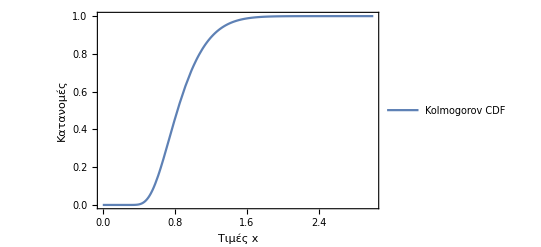

```mathematica
pkol2= Plot[Quiet[f[x]],{x,0,3},Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"Kolmogorov CDF"}]
```

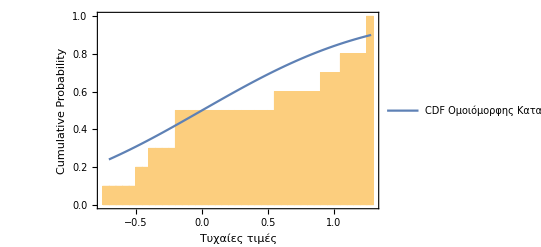

```mathematica
h1=Show[Histogram[X,50,"CDF",PlotRange->All],Plot[CDF[NormalDistribution[0,1],x],{x,Min[X],Max[X]},PlotRange->All,PlotLegends->{"CDF Ομοιόμορφης Κατανομής"}],Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-1.png",Show[h1,ImageSize->15 inches]];
```

```mathematica
DX=Max[Abs[Range[0,n-1]/n-CDF[NormalDistribution[0,1],Sort@X]]]
```

0.240785

```mathematica
KolmogorovSmirnovTest[X,NormalDistribution[0,1],"TestStatistic"]
```

0.240785

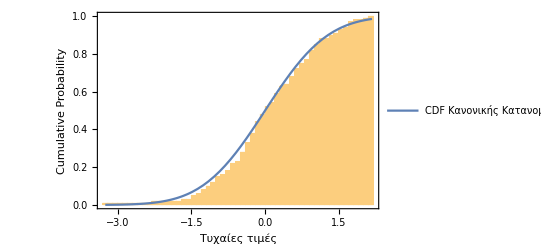

```mathematica
h2=Show[Histogram[X100,50,"CDF",PlotRange->All],Plot[CDF[NormalDistribution[0,1],x],{x,Min[X100],Max[X100]},PlotRange->All,PlotLegends->{"CDF Κανονικής Κατανομής"}],Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-2.png",Show[h2,ImageSize->15 inches]];
```

```mathematica
DX100=Max[Abs[Range[1,Length[X100]]/Length[X100]-CDF[NormalDistribution[0,1],Sort@X100]]]
```

0.0735278

```mathematica
KolmogorovSmirnovTest[X100,NormalDistribution[0,1],"TestStatistic"]
```

0.0835278

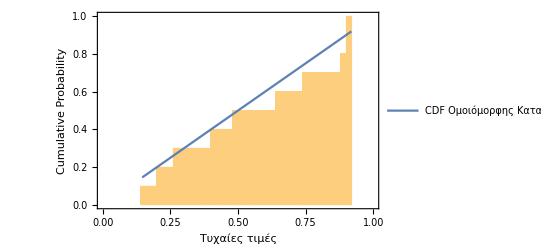

```mathematica
h3=Show[Histogram[Y,50,"CDF",PlotRange->{{0,1},{0,1}}],Plot[CDF[UniformDistribution[{0,1}],x],{x,Min[Y],Max[Y]},PlotLegends->{"CDF Ομοιόμορφης Κατανομής"},PlotRange->{{0,2},{0,1}}],Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-3.png",Show[h3,ImageSize->15 inches]];
```

```mathematica
DY =Max[Abs[Range[1,Length[Y]]/Length[Y]-CDF[UniformDistribution[{0,1}],Sort@Y]]] (*KolmogorovSmirnovTest[Y,UniformDistribution[{0,1}],"TestStatistic"]*)
```

0.0810923

```mathematica
KolmogorovSmirnovTest[Y,UniformDistribution[{0,1}],"TestStatistic"]
```

0.181092

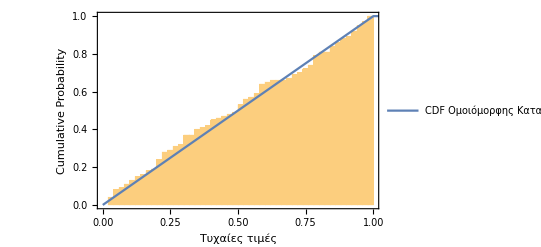

```mathematica
h4=Show[Histogram[Y100,50,"CDF",PlotRange->{{0,1},{0,1}}],Plot[CDF[UniformDistribution[{0,1}],x],{x,0,10},PlotLegends->{"CDF Ομοιόμορφης Κατανομής"},PlotRange->{{0,2},{0,1}},PlotRange->All],Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-4.png",Show[h4,ImageSize->15 inches]];
```

```mathematica
DY100 =Max[Abs[Range[1,Length[Y100]]/Length[Y100 ]-CDF[UniformDistribution[{0,1}],Sort@Y100]]] (*KolmogorovSmirnovTest[Y,UniformDistribution[{0,1}],"TestStatistic"]*)
```

0.0557888

```mathematica
KolmogorovSmirnovTest[Y100,UniformDistribution[{0,1}],"TestStatistic"]
```

0.0557888

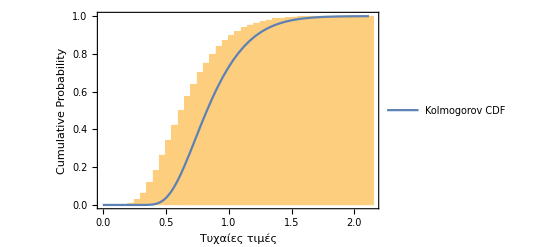

```mathematica
X10k = ParallelTable[
X = RandomVariate[NormalDistribution[0,1],n];
Max[Abs[Range[1,n]/n-CDF[NormalDistribution[0,1],Sort@X]]]*Sqrt[n],
{i,10000}];
hnorm1= Show[Histogram[X10k,50,"CDF"],Plot[Quiet[f[x]],{x,0,Max[X10k]},Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"Kolmogorov CDF"}],PlotRange->All,Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex5-5.png",Show[hnorm1,ImageSize->15 inches]];
```

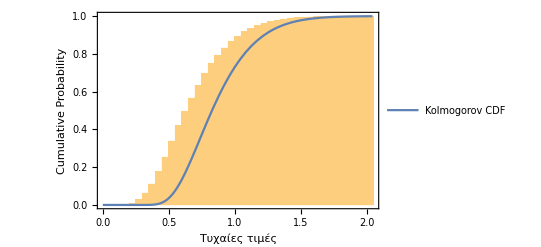

```mathematica
Y10k = ParallelTable[
Y = RandomVariate[UniformDistribution[{0,1}],n];
Max[Abs[Range[1,Length[Y]]/Length[Y]-CDF[UniformDistribution[{0,1}],Sort@Y]]],
{i,10000}]*Sqrt[n];
huni1 = Show[Histogram[Y10k,50,"CDF"],Plot[Quiet[f[x]],{x,0,Max[Y10k]},Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"Kolmogorov CDF"}],PlotRange->All,Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"NormalDistribution PDF"}]
Export["ex5-6.png",Show[huni1,ImageSize->15 inches]];
```

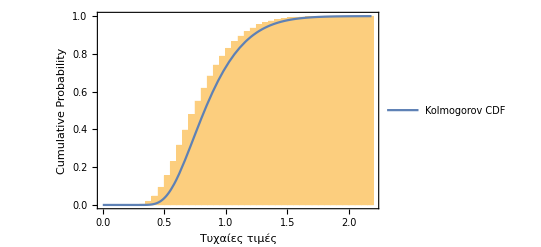

```mathematica
X100k = ParallelTable[
X = RandomVariate[NormalDistribution[0,1],ndot];
Max[Abs[Range[1,Length[X]]/Length[X]-CDF[NormalDistribution[0,1],Sort@X]]],
{i,10000}]*Sqrt[ndot];
hnorm100 = Show[Histogram[X100k,50,"CDF"],Plot[Quiet[f[x]],{x,0,Max[X100k]},Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"Kolmogorov CDF"}],PlotRange->All,Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"NormalDistribution PDF"}]
Export["ex5-7.png",Show[hnorm100,ImageSize->15 inches]];
```

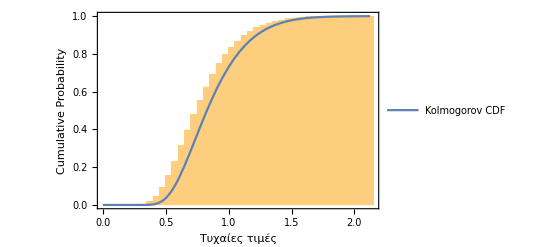

```mathematica
Y100k = ParallelTable[
Y = RandomVariate[UniformDistribution[{0,1}],ndot];
Max[Abs[Range[1,Length[Y]]/Length[Y]-CDF[UniformDistribution[{0,1}],Sort@Y]]],
{i,10000}]*Sqrt[ndot];
huni100 = Show[Histogram[Y100k,50,"CDF"],Plot[Quiet[f[x]],{x,0,Max[Y100k]},Frame->True,FrameLabel->{"Τιμές x","Κατανομές"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"Kolmogorov CDF"}],PlotRange->All,Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"NormalDistribution PDF"}]
Export["ex5-8.png",Show[huni100,ImageSize->15 inches]];
```

```mathematica
NPDFDIST[x_] := PDF[NormalDistribution[],x];
```

```mathematica
UPDFDIST[x_]:= PDF[UniformDistribution[{0,1}],x];
```

```mathematica
PVALUEX =Quiet[ SurvivalFunction[ChiSquareDistribution[n],Total[(CDF[NormalDistribution[0,1],Sort@X]- CDF[EmpiricalDistribution[X],X])^2/CDF[EmpiricalDistribution[X],X]]]]
```

0.461143

```mathematica
PVALUEX100 =SurvivalFunction[ChiSquareDistribution[ndot],Total[(CDF[NormalDistribution[0,1],Sort@X100]- CDF[EmpiricalDistribution[X100],X100])^2/CDF[EmpiricalDistribution[X100],X100]]]
```

0.0431335

```mathematica
PVALUEY =Quiet[ SurvivalFunction[ChiSquareDistribution[n],Total[(CDF[NormalDistribution[0,1],Sort@Y]- CDF[EmpiricalDistribution[Y],Y])^2/CDF[EmpiricalDistribution[Y],Y]]]]
```

0.689657

```mathematica
PVALUEY100 =SurvivalFunction[ChiSquareDistribution[ndot],Total[(CDF[NormalDistribution[0,1],Sort@Y100]- CDF[EmpiricalDistribution[Y100],Y100])^2/CDF[EmpiricalDistribution[Y100],Y100]]]
```

8.95987×10^-6

```mathematica
X500k = ParallelTable[
X = RandomVariate[NormalDistribution[0,1],500];
Max[Abs[Range[1,Length[X]]/Length[X]-CDF[NormalDistribution[0,1],Sort@X]]],
{i,10000}]*Sqrt[500];
```

```mathematica
PearsonChiSquareTest[X,NormalDistribution[],"PValue"]
```

0.347105

```mathematica
KolmogorovSmirnovTest[X,NormalDistribution[],"PValue"]
```

0.531389

```mathematica
PearsonChiSquareTest[X100,NormalDistribution[],"PValue"]
```

0.882877

```mathematica
KolmogorovSmirnovTest[X100,NormalDistribution[],"PValue"]
```

0.463151

```mathematica
PearsonChiSquareTest[Y,UniformDistribution[{0,1}],"PValue"]
```

0.849145

```mathematica
KolmogorovSmirnovTest[Y,UniformDistribution[{0,1}],"PValue"]
```

0.842273

```mathematica
PearsonChiSquareTest[Y100,UniformDistribution[{0,1}],"PValue"]
```

0.68576

```mathematica
KolmogorovSmirnovTest[Y100,UniformDistribution[{0,1}],"PValue"]
```

0.897358

```mathematica
pemp1=Plot[CDF[EmpiricalDistribution[X10k],x],{x,0,3},PlotRange->Full,PlotStyle->Green,PlotLegends->{"n = 10"},Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20}];
```

```mathematica
pemp2=Plot[CDF[EmpiricalDistribution[X100k],x],{x,0,3},PlotRange->Full,PlotStyle->Red,PlotLegends->{"n = 100"},Frame->True,FrameLabel->{"Τυχαίες τιμές","Cumulative Probability"},LabelStyle->{FontFamily->"Times New Roman",20}];
```

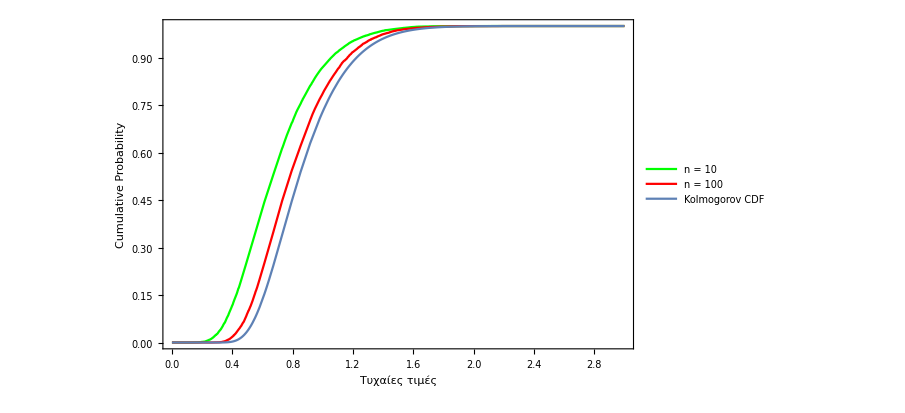

```mathematica
sh1=Show[pemp1,pemp2,pkol2]
Export["ex5-9.png",Show[sh1,ImageSize->15 inches]];
```

```mathematica
histogram1=Histogram[Y100k,50,"CDF"];
bincentersandheights1=Cases[histogram1,Rectangle[{xmin_,ymin_},{xmax_,ymax_},___]:>{Mean[{xmin,xmax}],ymax},All];
Y100kobs =ParallelTable[bincentersandheights1[[i]][[2]],{i,1,Length[bincentersandheights1]}];
Y100kx = ParallelTable[bincentersandheights1[[i]][[1]],{i,1,Length[bincentersandheights1]}];

Show[histogram1,pkol2,ListLinePlot[bincentersandheights1,PlotStyle->Directive[Thick,Red],PlotMarkers->"●"]]
```

-Graphics-

```mathematica
histogram2=Histogram[Y10k,50,"CDF"];
bincentersandheights2=Cases[histogram2,Rectangle[{xmin_,ymin_},{xmax_,ymax_},___]:>{Mean[{xmin,xmax}],ymax},All];
Show[histogram2,pkol2,ListLinePlot[bincentersandheights2,PlotStyle->Directive[Thick,Red],PlotMarkers->"●"]]
Y10kobs =ParallelTable[bincentersandheights2[[i]][[2]],{i,1,Length[bincentersandheights2]}];
Y10kx = ParallelTable[bincentersandheights2[[i]][[1]],{i,1,Length[bincentersandheights2]}];
PVALUEY10k =Quiet[SurvivalFunction[ChiSquareDistribution[10],Total[CDF[EmpiricalDistribution[X100k],X100k] - f[X100k]]]]
```

-Graphics-

1.61543×10^-149

```mathematica
dist=ProbabilityDistribution[{"CDF",f[x]},{x,-∞,∞}];
```

```mathematica
data=RandomVariate[NormalDistribution[],50];
```

```mathematica
KolmogorovSmirnovTest[Y10k,dist,"TestStatistic"]
```

1.

```mathematica
PVALUEY10k =Quiet[SurvivalFunction[ChiSquareDistribution[10],Total[(CDF[EmpiricalDistribution[Y10k],Y10kx] - Y10kobs)^2/Y10kobs]]]//N
```

1.

```mathematica
Length[Y100kx]
```

38

```mathematica
Total[(CDF[EmpiricalDistribution[Y10k],Y10kx] - Y10kobs)^2/Y10kobs]
```

0.0545114

```mathematica
Total[(CDF[EmpiricalDistribution[X10k],Y100kx] - Y100kobs)^2/Y100kobs]
```

2.64915

```mathematica
Quiet[SurvivalFunction[ChiSquareDistribution[100],90]]//N
```

0.753198

```mathematica
Total[(CDF[EmpiricalDistribution[Y100k],Y100kx] -Y100kobs)^2/Y100kobs]
```

0.0548675

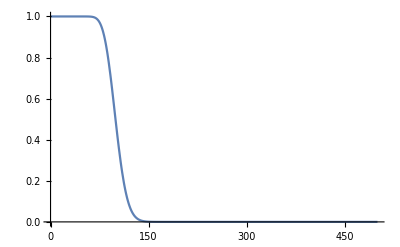

```mathematica
Plot[SurvivalFunction[ChiSquareDistribution[100],x],{x,0,500}]
```

```mathematica
Quiet[SurvivalFunction[ChiSquareDistribution[100],0.05451135542766338*Sqrt[100]*100]]//N
```

0.99994

```mathematica
Total[(CDF[EmpiricalDistribution[Y10k],Y10kx] - Y10kobs)^2/Y10kobs]
```

0.0545114

```mathematica
Total[(CDF[EmpiricalDistribution[Y10k],Y10kx] - Y10kobs)^2/Y10kobs]
```

```mathematica
Quiet[SurvivalFunction[ChiSquareDistribution[10],0.05486748608711086*Sqrt[10]*100]]//N
```

0.0669568

```mathematica
Total[(CDF[EmpiricalDistribution[Y100k],Y100kx] - Y100kobs)^2/Y100kobs]
```

0.0548675

```mathematica
Sqrt[10]//N
```

3.16228

```mathematica
histogram3=Histogram[X10k,50,"CDF"];
bincentersandheights3=Cases[histogram3,Rectangle[{xmin_,ymin_},{xmax_,ymax_},___]:>{Mean[{xmin,xmax}],ymax},All];
Show[histogram3,pkol2,ListLinePlot[bincentersandheights3,PlotStyle->Directive[Thick,Red],PlotMarkers->"●"]]
X10kobs =ParallelTable[bincentersandheights3[[i]][[2]],{i,1,Length[bincentersandheights3]}];
X10kx = ParallelTable[bincentersandheights3[[i]][[1]],{i,1,Length[bincentersandheights3]}];
```

-Graphics-

```mathematica
Quiet[SurvivalFunction[ChiSquareDistribution[100],1.1576125235952477*80]]//N
```

0.687446

```mathematica
0
```

```mathematica
Total[(CDF[EmpiricalDistribution[X100k],X100kx] - X100kobs)^2/X100kobs]
```

1.15761

```mathematica
histogram4=Histogram[X10k,50,"CDF"];
bincentersandheights4=Cases[histogram3,Rectangle[{xmin_,ymin_},{xmax_,ymax_},___]:>{Mean[{xmin,xmax}],ymax},All];
Show[histogram4,pkol2,ListLinePlot[bincentersandheights4,PlotStyle->Directive[Thick,Red],PlotMarkers->"●"]]
X100kobs =ParallelTable[bincentersandheights4[[i]][[2]],{i,1,Length[bincentersandheights4]}];
X100kx = ParallelTable[bincentersandheights4[[i]][[1]],{i,1,Length[bincentersandheights4]}];
```

-Graphics-

```mathematica
Quiet[SurvivalFunction[ChiSquareDistribution[10],0.05349547185536954*100]]//N
```

0.866639

```mathematica
Total[(CDF[EmpiricalDistribution[X10k],X10kx] - X10kobs)^2/X10kobs]
```

0.0534955